```mathematica
pic = CurrentImage[]
```

-Graphics-

```mathematica
ColorNegate[pic]
```

-Graphics-

```mathematica
ImageCollage[Table[Blur[ColorNegate[data], n], {n, 0, 15}]]
```

-Graphics-

```mathematica
DominantColors[data]
```

{RGBColor[0.0753071996192328, 0.06878898666021707, 0.07462874002119815],RGBColor[0.29933251232538577, 0.20959655889284112, 0.16386663854005498],RGBColor[0.5987052769524405, 0.5646986092961668, 0.5199086451819671],RGBColor[0.34897911237853874, 0.3520308442342637, 0.3614187029328741],RGBColor[0.6687621077509657, 0.5004425502568937, 0.34870955836279144],RGBColor[0.986277541385341, 0.9857820562628915, 0.9855274827361383],RGBColor[0.5471718720414002, 0.3210538093574782, 0.2766688048994442]}

```mathematica
Binarize[data]
```

-Graphics-

```mathematica
EdgeDetect[data]
```

-Graphics-

```mathematica
Manipulate[Binarize[data, t], {t, 0, 1}]
```

Binarize::imginv: Expecting an image or graphics instead of data.

```mathematica
LinguisticAssistant
```

planets

```mathematica
planets = LinguisticAssistant
```

planets

```mathematica
EntityList[planets]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
EntityValue[planets, "Image"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

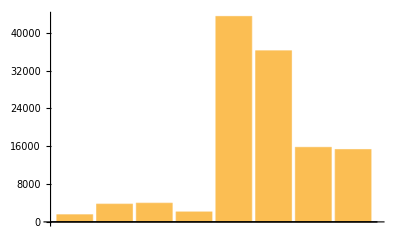

```mathematica
BarChart[EntityValue[planets, "Radius"]]
```

```mathematica
EntityValue[planets, "Radius"]
```

{1516. mi,3760.4 mi,3958.761 mi,2106.1 mi,43441. mi,36184. mi,15759. mi,15299. mi}

```mathematica
text="This is the sentence that I will use to show what you can do with text in
Mathematica."
```

This is the sentence that I will use to show what you can do with text in
Mathematica.

```mathematica
Characters[text]
```

{T,h,i,s, ,i,s, ,t,h,e, ,s,e,n,t,e,n,c,e, ,t,h,a,t, ,I, ,w,i,l,l, ,u,s,e, ,t,o, ,s,h,o,w, ,w,h,a,t, ,y,o,u, ,c,a,n, ,d,o, ,w,i,t,h, ,t,e,x,t, ,i,n,
,M,a,t,h,e,m,a,t,i,c,a,.}

```mathematica
Sort[Characters[text]]
```

{.,
, , , , , , , , , , , , , , , , ,a,a,a,a,a,a,c,c,c,d,e,e,e,e,e,e,e,h,h,h,h,h,h,h,i,i,i,i,i,i,I,l,l,m,M,n,n,n,n,o,o,o,o,s,s,s,s,s,t,t,t,t,t,t,t,t,t,t,t,T,u,u,w,w,w,w,x,y}

```mathematica
WordCloud[Characters[text]]
```

-Graphics-

```mathematica
Rasterize[Style[text,38,Red]]
```

-Graphics-

```mathematica
AnatomyData[LinguisticAssistant, "Image"]
```

-Graphics-

```mathematica
Export["brain.stl",LinguisticAssistant["Graphics3D"],{"STL", "BinaryFormat" -> False}]
```

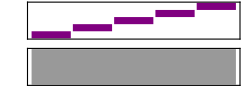

```mathematica
Sound[Table[SoundNote[n],{n,5}]]
```

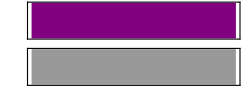

```mathematica
Sound[SoundNote["C"]]
```

```mathematica
Sound[SoundNote["C"]]
```

-Graphics-

```mathematica
Play[Sin[256*2 π t],{t,0,1}]
```

-Graphics-

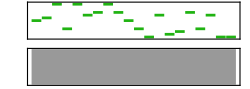

```mathematica
Sound[Table[SoundNote[RandomInteger[12],1,"Banjo"],20]]
```

```mathematica
(*This is my Cloud Deployed function for the show of data*)
CloudDeploy[Manipulate[Sound[Table[SoundNote[RandomInteger[{notes}],length,"Guitar"],20]],{notes,0,12, 1},{length,.1,1}], Permissions->"Public"]
```

CloudObject[]